### Start choosing the example:

```mathematica
t=28;
beta = 1;
A = 0.2;
```

### DataToEquations and the critical congestion solver

```mathematica
Data=DataG[t];
MFGEquations=DataToEquations[Data];//Timing
```

DataToEquations: Finished assembling strucural equations. Reducing the structural system ...

DataToEquations: Critical case ...

DataToEquations: Critical congestion solved.

DataToEquations: Done.

{0.307262,Null}

```mathematica
Map[Simplify,MFGEquations["criticalreduced1"][[2]]//KeySort]
```

<|j14→0,j15→3/2,j16→1/2,j17→1/2,j18→2,j19→3/2,j20→0,j21→0,j22→0,j23→0,jt24→3/2,jt25→0,jt26→0,jt27→0,jt28→0,jt29→0,jt30→3/2,jt31→1/2,jt32→1/2,jt33→0,u34→4,u35→4,u36→11/2,u37→5,u38→11/2,u39→11/2,u40→4,u41→5,u42→5,u43→11/2|>

```mathematica
Data
```

<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{0,0,0}},Entrance Vertices and Currents→{{2,2}},Exit Vertices and Terminal Costs→{{1,4},{3,5}},Switching Costs→{}|>

#### Non-linear case

```mathematica
alpha = 0;(*when we decide that we really want to solve this, try adaptivity in the alpha*)
FFR=Map[Simplify,Catch @ FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort]
```

FRX1: The Error on the nonlinear terms is 0.186322

FRX1: The Error on the nonlinear terms is 0.0908376

FRX1: The Error on the nonlinear terms is 0.012649

FRX1: The Error on the nonlinear terms is 0.00156525

FRX1: The Error on the nonlinear terms is 0.000228207

FRX1: The Error on the nonlinear terms is 0.0000326905

FRX1: The Error on the nonlinear terms is 4.69514×10^-6

FRX1: The Error on the nonlinear terms is 6.74082×10^-7

FRX1: The Error on the nonlinear terms is 9.67834×10^-8

FRX1: The Error on the nonlinear terms is 1.38959×10^-8

<|j14→0,j15→1.88235,j16→0.117647,j17→0.117647,j18→2,j19→1.88235,j20→0,j21→0,j22→0,j23→0,jt24→1.88235,jt25→0,jt26→0,jt27→0,jt28→0,jt29→0,jt30→1.88235,jt31→0.117647,jt32→0.117647,jt33→0,u34→4.,u35→4,u36→5.51282,u37→5,u38→5.51282,u39→5.51282,u40→4,u41→5.,u42→5,u43→5.51282|>

```mathematica
FFR
```

```mathematica
alpha = 0.001;
FFR=Catch@FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Error on the nonlinear terms is 0.186038

FRX1: The Error on the nonlinear terms is 0.0905313

FRX1: The Error on the nonlinear terms is 0.0126803

FRX1: The Error on the nonlinear terms is 0.0015427

FRX1: The Error on the nonlinear terms is 0.000221903

FRX1: The Error on the nonlinear terms is 0.0000313599

FRX1: The Error on the nonlinear terms is 4.44331×10^-6

FRX1: The Error on the nonlinear terms is 6.29333×10^-7

FRX1: The Error on the nonlinear terms is 8.91409×10^-8

FRX1: The Error on the nonlinear terms is 1.26261×10^-8

<|j14→0,j15→1.88201,j16→2-1.88201,j17→2-1.88201,j18→2,j19→1.88201,j20→0,j21→0,j22→0,j23→0,jt24→1.88201,jt25→0,jt26→0,jt27→0,jt28→0,jt29→0,jt30→1.88201,jt31→2-1.88201,jt32→2-1.88201,jt33→0,u34→4.,u35→4,u36→5.51295,u37→5,u38→5.51295,u39→-0.369068+1. 1.88201+1. 4.,u40→4,u41→-2.39496+1. 1.88201+1. 5.51295,u42→5,u43→5.51295|>

```mathematica
alpha = 0.1;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],20,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Error on the nonlinear terms is 0.158453

FRX1: The Error on the nonlinear terms is 0.0654848

FRX1: The Error on the nonlinear terms is 0.0123881

FRX1: The Error on the nonlinear terms is 0.000418052

FRX1: The Error on the nonlinear terms is 3.73787×10^-6

FRX1: The Error on the nonlinear terms is 3.04315×10^-8

FRX1: The Error on the nonlinear terms is 2.47538×10^-10

FRX1: The Error on the nonlinear terms is 2.01348×10^-12

FRX1: The Error on the nonlinear terms is 1.60936×10^-14

FRX1: The Error on the nonlinear terms is 2.48253×10^-16

FRX1: The Error on the nonlinear terms is 2.48253×10^-16

<|j14→0,j15→1.84621,j16→2-1.84621,j17→2-1.84621,j18→2,j19→1.84621,j20→0,j21→0,j22→0,j23→0,jt24→1.84621,jt25→0,jt26→0,jt27→0,jt28→0,jt29→0,jt30→1.84621,jt31→2-1.84621,jt32→2-1.84621,jt33→0,u34→4.,u35→4,u36→5.5243,u37→5,u38→5.5243,u39→-0.321902+1. 1.84621+1. 4.,u40→4,u41→-2.37051+1. 1.84621+1. 5.5243,u42→5,u43→5.5243|>

```mathematica
alpha = 0.9;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Error on the nonlinear terms is 0.00303532

FRX1: The Error on the nonlinear terms is 0.000151158

FRX1: The Error on the nonlinear terms is 7.28629×10^-6

FRX1: The Error on the nonlinear terms is 3.50633×10^-7

FRX1: The Error on the nonlinear terms is 1.68719×10^-8

FRX1: The Error on the nonlinear terms is 8.11842×10^-10

FRX1: The Error on the nonlinear terms is 3.90645×10^-11

FRX1: The Error on the nonlinear terms is 1.87916×10^-12

FRX1: The Error on the nonlinear terms is 9.04982×10^-14

FRX1: The Error on the nonlinear terms is 4.44644×10^-15

<|j14→0,j15→1.53162,j16→2-1.53162,j17→2-1.53162,j18→2,j19→1.53162,j20→0,j21→0,j22→0,j23→0,jt24→1.53162,jt25→0,jt26→0,jt27→0,jt28→0,jt29→0,jt30→1.53162,jt31→2-1.53162,jt32→2-1.53162,jt33→0,u34→4.,u35→4,u36→5.51333,u37→5,u38→5.51333,u39→-0.0182918+1. 1.53162+1. 4.,u40→4,u41→-2.04494+1. 1.53162+1. 5.51333,u42→5,u43→5.51333|>

```mathematica
alpha = 1;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Error on the nonlinear terms is 1.86107×10^-15

<|j14→0,j15→3/2,j16→2-3/2,j17→2-3/2,j18→2,j19→3/2,j20→0,j21→0,j22→0,j23→0,jt24→3/2,jt25→0,jt26→0,jt27→0,jt28→0,jt29→0,jt30→3/2,jt31→2-3/2,jt32→2-3/2,jt33→0,u34→4,u35→4,u36→11/2,u37→5,u38→11/2,u39→3/2+4,u40→4,u41→-2+3/2+11/2,u42→5,u43→11/2|>

```mathematica
alpha = 1.2;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Error on the nonlinear terms is 0.0374283

FRX1: The Error on the nonlinear terms is 0.0078923

FRX1: The Error on the nonlinear terms is 0.00170575

FRX1: The Error on the nonlinear terms is 0.000366699

FRX1: The Error on the nonlinear terms is 0.000078923

FRX1: The Error on the nonlinear terms is 0.000016982

FRX1: The Error on the nonlinear terms is 3.65426×10^-6

FRX1: The Error on the nonlinear terms is 7.86327×10^-7

FRX1: The Error on the nonlinear terms is 1.69203×10^-7

FRX1: The Error on the nonlinear terms is 3.64094×10^-8

<|j14→0,j15→1.41188,j16→2-1.41188,j17→2-1.41188,j18→2,j19→1.41188,j20→0,j21→0,j22→0,j23→0,jt24→1.41188,jt25→0,jt26→0,jt27→0,jt28→0,jt29→0,jt30→1.41188,jt31→2-1.41188,jt32→2-1.41188,jt33→0,u34→4.,u35→4,u36→5.61741,u37→5,u38→5.61741,u39→0.205527+1. 1.41188+1. 4.,u40→4,u41→-2.02929+1. 1.41188+1. 5.61741,u42→5,u43→5.61741|>

```mathematica
alpha = 1.5;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Error on the nonlinear terms is 0.421258

FRX1: The Error on the nonlinear terms is 0.298212

FRX1: The Error on the nonlinear terms is 0.22254

FRX1: The Error on the nonlinear terms is 0.159346

FRX1: The Error on the nonlinear terms is 0.117454

FRX1: The Error on the nonlinear terms is 0.0847023

FRX1: The Error on the nonlinear terms is 0.0620425

FRX1: The Error on the nonlinear terms is 0.0449232

FRX1: The Error on the nonlinear terms is 0.0327987

FRX1: The Error on the nonlinear terms is 0.023801

<|j14→0,j15→1.30174,j16→2-1.30174,j17→2-1.30174,j18→2,j19→1.30174,j20→0,j21→0,j22→0,j23→0,jt24→1.30174,jt25→0,jt26→0,jt27→0,jt28→0,jt29→0,jt30→1.30174,jt31→2-1.30174,jt32→2-1.30174,jt33→0,u34→4.,u35→4,u36→5.82373,u37→5,u38→5.82373,u39→0.52199+1. 1.30174+1. 4.,u40→4,u41→-2.12547+1. 1.30174+1. 5.82373,u42→5,u43→5.82373|>

```mathematica
alpha = 1.6;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Error on the nonlinear terms is 0.750532

FRX1: The Error on the nonlinear terms is 0.740547

FRX1: The Error on the nonlinear terms is 0.733422

FRX1: The Error on the nonlinear terms is 0.723203

FRX1: The Error on the nonlinear terms is 0.71587

FRX1: The Error on the nonlinear terms is 0.705449

FRX1: The Error on the nonlinear terms is 0.697925

FRX1: The Error on the nonlinear terms is 0.687335

FRX1: The Error on the nonlinear terms is 0.679642

FRX1: The Error on the nonlinear terms is 0.668918

<|j14→0,j15→1.47225,j16→2-1.47225,j17→2-1.47225,j18→2,j19→1.47225,j20→0,j21→0,j22→0,j23→0,jt24→1.47225,jt25→0,jt26→0,jt27→0,jt28→0,jt29→0,jt30→1.47225,jt31→2-1.47225,jt32→2-1.47225,jt33→0,u34→4.,u35→4,u36→5.85812,u37→5,u38→5.85812,u39→0.385865+1. 1.47225+1. 4.,u40→4,u41→-2.33037+1. 1.47225+1. 5.85812,u42→5,u43→5.85812|>

```mathematica
alpha = 1.6001;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],200,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Error on the nonlinear terms is 0.171333

FRX1: The Error on the nonlinear terms is 0.0613755

FRX1: The Error on the nonlinear terms is 0.0250073

FRX1: The Error on the nonlinear terms is 0.00969359

FRX1: The Error on the nonlinear terms is 0.00383233

FRX1: The Error on the nonlinear terms is 0.00150343

FRX1: The Error on the nonlinear terms is 0.000591597

FRX1: The Error on the nonlinear terms is 0.000232514

FRX1: The Error on the nonlinear terms is 0.0000914272

FRX1: The Error on the nonlinear terms is 0.0000359436

FRX1: The Error on the nonlinear terms is 0.0000141319

FRX1: The Error on the nonlinear terms is 5.55605×10^-6

FRX1: The Error on the nonlinear terms is 2.18442×10^-6

FRX1: The Error on the nonlinear terms is 8.58826×10^-7

FRX1: The Error on the nonlinear terms is 3.37656×10^-7

FRX1: The Error on the nonlinear terms is 1.32753×10^-7

FRX1: The Error on the nonlinear terms is 5.21931×10^-8

FRX1: The Error on the nonlinear terms is 2.05202×10^-8

FRX1: The Error on the nonlinear terms is 8.06773×10^-9

FRX1: The Error on the nonlinear terms is 3.17191×10^-9

FRX1: The Error on the nonlinear terms is 1.24707×10^-9

FRX1: The Error on the nonlinear terms is 4.90298×10^-10

FRX1: The Error on the nonlinear terms is 1.92766×10^-10

FRX1: The Error on the nonlinear terms is 7.57874×10^-11

FRX1: The Error on the nonlinear terms is 2.9797×10^-11

FRX1: The Error on the nonlinear terms is 1.17154×10^-11

FRX1: The Error on the nonlinear terms is 4.60661×10^-12

FRX1: The Error on the nonlinear terms is 1.81124×10^-12

FRX1: The Error on the nonlinear terms is 7.11577×10^-13

FRX1: The Error on the nonlinear terms is 2.7971×10^-13

FRX1: The Error on the nonlinear terms is 1.09759×10^-13

FRX1: The Error on the nonlinear terms is 4.31008×10^-14

FRX1: The Error on the nonlinear terms is 1.71032×10^-14

FRX1: The Error on the nonlinear terms is 6.88696×10^-15

FRX1: The Error on the nonlinear terms is 2.66511×10^-15

<|j14→0,j15→1.35729,j16→2-1.35729,j17→2-1.35729,j18→2,j19→1.35729,j20→0,j21→0,j22→0,j23→0,jt24→1.35729,jt25→0,jt26→0,jt27→0,jt28→0,jt29→0,jt30→1.35729,jt31→2-1.35729,jt32→2-1.35729,jt33→0,u34→4.,u35→4,u36→5.36983,u37→5,u38→5.36983,u39→0.0125366+1. 1.35729+1. 4.,u40→4,u41→-1.72711+1. 1.35729+1. 5.36983,u42→5,u43→5.36983|>

```mathematica
alpha = 2;
FixedPoint[FixedReduceX1[MFGEquations],FFR,20,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Error on the nonlinear terms is 0.159239

FRX1: The Error on the nonlinear terms is 0.115173

FRX1: The Error on the nonlinear terms is 0.0864928

FRX1: The Error on the nonlinear terms is 0.063129

FRX1: The Error on the nonlinear terms is 0.0470375

FRX1: The Error on the nonlinear terms is 0.0345098

FRX1: The Error on the nonlinear terms is 0.0256064

FRX1: The Error on the nonlinear terms is 0.0188409

FRX1: The Error on the nonlinear terms is 0.0139488

FRX1: The Error on the nonlinear terms is 0.0102798

FRX1: The Error on the nonlinear terms is 0.00760142

FRX1: The Error on the nonlinear terms is 0.00560689

FRX1: The Error on the nonlinear terms is 0.00414331

FRX1: The Error on the nonlinear terms is 0.00305761

FRX1: The Error on the nonlinear terms is 0.00225867

FRX1: The Error on the nonlinear terms is 0.00166726

FRX1: The Error on the nonlinear terms is 0.00123137

FRX1: The Error on the nonlinear terms is 0.000909075

FRX1: The Error on the nonlinear terms is 0.000671337

FRX1: The Error on the nonlinear terms is 0.000495662

<|j14→0,j15→1.30387,j16→2-1.30387,j17→2-1.30387,j18→2,j19→1.30387,j20→0,j21→0,j22→0,j23→0,jt24→1.30387,jt25→0,jt26→0,jt27→0,jt28→0,jt29→0,jt30→1.30387,jt31→2-1.30387,jt32→2-1.30387,jt33→0,u34→4.,u35→4,u36→5.23823,u37→5,u38→5.23823,u39→-0.0656368+1. 1.30387+1. 4.,u40→4,u41→-1.5421+1. 1.30387+1. 5.23823,u42→5,u43→5.23823|>

```mathematica
alpha = 1.605;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Error on the nonlinear terms is 0.771472

FRX1: The Error on the nonlinear terms is 0.774695

FRX1: The Error on the nonlinear terms is 0.777005

FRX1: The Error on the nonlinear terms is 0.780437

FRX1: The Error on the nonlinear terms is 0.782892

FRX1: The Error on the nonlinear terms is 0.786551

FRX1: The Error on the nonlinear terms is 0.789164

FRX1: The Error on the nonlinear terms is 0.793071

FRX1: The Error on the nonlinear terms is 0.795855

FRX1: The Error on the nonlinear terms is 0.800031

<|j14→0,j15→1.50949,j16→2-1.50949,j17→2-1.50949,j18→2,j19→1.50949,j20→0,j21→0,j22→0,j23→0,jt24→1.50949,jt25→0,jt26→0,jt27→0,jt28→0,jt29→0,jt30→1.50949,jt31→2-1.50949,jt32→2-1.50949,jt33→0,u34→4.,u35→4,u36→5.86167,u37→5,u38→5.86167,u39→0.352181+1. 1.50949+1. 4.,u40→4,u41→-2.37116+1. 1.50949+1. 5.86167,u42→5,u43→5.86167|>

```mathematica
alpha = 1.61;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Error on the nonlinear terms is 0.792915

FRX1: The Error on the nonlinear terms is 0.810472

FRX1: The Error on the nonlinear terms is 0.823116

FRX1: The Error on the nonlinear terms is 0.842587

FRX1: The Error on the nonlinear terms is 0.856473

FRX1: The Error on the nonlinear terms is 0.878233

FRX1: The Error on the nonlinear terms is 0.89359

FRX1: The Error on the nonlinear terms is 0.918126

FRX1: The Error on the nonlinear terms is 0.935248

FRX1: The Error on the nonlinear terms is 0.963202

<|j14→0,j15→1.5552,j16→2-1.5552,j17→2-1.5552,j18→2,j19→1.5552,j20→0,j21→0,j22→0,j23→0,jt24→1.5552,jt25→0,jt26→0,jt27→0,jt28→0,jt29→0,jt30→1.5552,jt31→2-1.5552,jt32→2-1.5552,jt33→0,u34→4.,u35→4,u36→5.86869,u37→5,u38→5.86869,u39→0.313492+1. 1.5552+1. 4.,u40→4,u41→-2.42388+1. 1.5552+1. 5.86869,u42→5,u43→5.86869|>

```mathematica
alpha = 1.62;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Error on the nonlinear terms is 0.837365

FRX1: The Error on the nonlinear terms is 0.887302

FRX1: The Error on the nonlinear terms is 0.92359

FRX1: The Error on the nonlinear terms is 0.983876

FRX1: The Error on the nonlinear terms is 1.02656

FRX1: The Error on the nonlinear terms is 1.10133

FRX1: The Error on the nonlinear terms is 1.15284

FRX1: The Error on the nonlinear terms is 1.24896

FRX1: The Error on the nonlinear terms is 1.31339

FRX1: The Error on the nonlinear terms is 1.44333

<|j14→0,j15→1.68476,j16→2-1.68476,j17→2-1.68476,j18→2,j19→1.68476,j20→0,j21→0,j22→0,j23→0,jt24→1.68476,jt25→0,jt26→0,jt27→0,jt28→0,jt29→0,jt30→1.68476,jt31→2-1.68476,jt32→2-1.68476,jt33→0,u34→4.,u35→4,u36→5.90537,u37→5,u38→5.90537,u39→0.22061+1. 1.68476+1. 4.,u40→4,u41→-2.59013+1. 1.68476+1. 5.90537,u42→5,u43→5.90537|>

```mathematica
alpha = 1.65;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Error on the nonlinear terms is 0.984284

FRX1: The Error on the nonlinear terms is 1.16863

FRX1: The Error on the nonlinear terms is 1.30674

FRX1: The Error on the nonlinear terms is 1.60536

FRX1: The Error on the nonlinear terms is 1.81994

FRX1: The Error on the nonlinear terms is 2.40346

FRX1: The Error on the nonlinear terms is 2.87194

FRX1: The Error on the nonlinear terms is 3.24475

FRX1: The Error on the nonlinear terms is 3.70382

FRX1: The Error on the nonlinear terms is 3.70382

<|j14→0,j15→2.,j16→2-2.,j17→2-2.,j18→2,j19→2.,j20→0,j21→0,j22→0,j23→0,jt24→2.,jt25→0,jt26→0,jt27→0,jt28→0,jt29→0,jt30→2.,jt31→2-2.,jt32→2-2.,jt33→0,u34→4.,u35→4,u36→6.00694,u37→5,u38→6.00694,u39→0.00693559+1. 2.+1. 4.,u40→4,u41→-4.42578+1. 2.+1. 6.00694,u42→5,u43→6.00694|>

```mathematica
alpha = 1.7;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Error on the nonlinear terms is 1.28376

FRX1: The Error on the nonlinear terms is 1.89762

FRX1: The Error on the nonlinear terms is 2.43903

FRX1: The Error on the nonlinear terms is 3.59892

FRX1: The Error on the nonlinear terms is 4.7667

FRX1: The Error on the nonlinear terms is 4.7667

FRX1: The Error on the nonlinear terms is 4.7667

«3 more identical outputs»

<|j14→0,j15→2.,j16→2-2.,j17→2-2.,j18→2,j19→2.,j20→0,j21→0,j22→0,j23→0,jt24→2.,jt25→0,jt26→0,jt27→0,jt28→0,jt29→0,jt30→2.,jt31→2-2.,jt32→2-2.,jt33→0,u34→4.,u35→4,u36→6.,u37→5,u38→6.,u39→0.+1. 2.+1. 4.,u40→4,u41→-5.37057+1. 2.+1. 6.,u42→5,u43→6.|>

```mathematica
alpha = 1.8;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Error on the nonlinear terms is 2.24017

FRX1: The Error on the nonlinear terms is 5.07141

FRX1: The Error on the nonlinear terms is 7.05822

FRX1: The Error on the nonlinear terms is 7.05822

FRX1: The Error on the nonlinear terms is 7.05822

«5 more identical outputs»

<|j14→0,j15→2.,j16→2-2.,j17→2-2.,j18→2,j19→2.,j20→0,j21→0,j22→0,j23→0,jt24→2.,jt25→0,jt26→0,jt27→0,jt28→0,jt29→0,jt30→2.,jt31→2-2.,jt32→2-2.,jt33→0,u34→4.,u35→4,u36→6.,u37→5,u38→6.,u39→0.+1. 2.+1. 4.,u40→4,u41→-6.99091+1. 2.+1. 6.,u42→5,u43→6.|>

```mathematica
alpha = 1.9;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Error on the nonlinear terms is 4.95644

FRX1: The Error on the nonlinear terms is 8.99242

FRX1: The Error on the nonlinear terms is 11.164

FRX1: The Error on the nonlinear terms is 11.164

FRX1: The Error on the nonlinear terms is 11.164

«5 more identical outputs»

<|j14→0,j15→2.,j16→2-2.,j17→2-2.,j18→2,j19→2.,j20→0,j21→0,j22→0,j23→0,jt24→2.,jt25→0,jt26→0,jt27→0,jt28→0,jt29→0,jt30→2.,jt31→2-2.,jt32→2-2.,jt33→0,u34→4.,u35→4,u36→6.,u37→5,u38→6.,u39→0.+1. 2.+1. 4.,u40→4,u41→-9.89413+1. 2.+1. 6.,u42→5,u43→6.|>

```mathematica
alpha = 2;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],20,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Error on the nonlinear terms is 14.698

FRX1: The Error on the nonlinear terms is 20.3268

FRX1: The Error on the nonlinear terms is 20.3268

FRX1: The Error on the nonlinear terms is 20.3268

«16 more identical outputs»

<|j14→0,j15→2.,j16→2-2.,j17→2-2.,j18→2,j19→2.,j20→0,j21→0,j22→0,j23→0,jt24→2.,jt25→0,jt26→0,jt27→0,jt28→0,jt29→0,jt30→2.,jt31→2-2.,jt32→2-2.,jt33→0,u34→4.,u35→4,u36→6.,u37→5,u38→6.,u39→0.+1. 2.+1. 4.,u40→4,u41→-16.3732+1. 2.+1. 6.,u42→5,u43→6.|>

### What we this plot for?

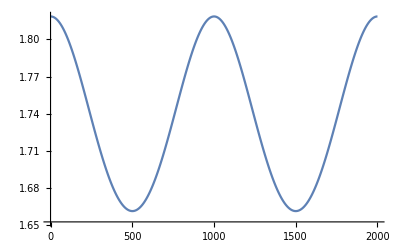

```mathematica
ListLinePlot [Values @ First @ FindRoot [Parameters["H[x,p,m]"][#,-2/(m^(1-.5)),m],{m,1}]& /@Table[i,{i,0,1,1/2000}]]
```

j from critical cong. use this in the rhs. maybe some jt is now defined and changes the value of that initial j. so, if we use the association to update the solution rules, we will alwas retrieve the most up - to - date values.